```mathematica
Clear["Global`*"]
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
mup[k_]=Sqrt[(k+1)*(Np-k)];
mdown[k_]=Sqrt[k*(Np-k+1)];
gamma=0.2;
eqn[k1_,k2_]=psi[k1,k2]'[t]==-I*(mup[k1]*mup[k2]*psi[k1+1,k2+1][t]+mdown[k1]*mdown[k2]*psi[k1-1,k2-1][t]+gamma);
pinitial[k1_,k2_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2];
rho$mixed[t_]:=ArrayFlatten[Table[Sum[psol[k1, k2][t]*Conjugate[psol[k1p, k2][t]], {k2, 0, Np}], {k1, 0, Np},{k1p, 0, Np}]];
```

```mathematica
Np=5; tmax=2.0*Pi;
vars={};
equations={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations=Append[equations,eqn[k1,k2]];
];
];
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations=Append[equations,psi[k1,k2][0]==pinitial[k1,k2]];
vars=Append[vars,psi[k1,k2]];
];
];
solutions=NDSolve[equations,vars,{t,0,tmax}];
Clear[k1,k2];
psoltemp[k1_,k2_]:=psi[k1,k2]/.solutions[[1]][[k1*(Np+1)+k2+1]];
psol[k1_,k2_]:=Function[τ,psoltemp[k1,k2][τ]];
```

```mathematica
(*Now repeating for pure initial state*)
pinitial$p[k1_,k2_]=If[(k1==Np)&&(k2==Np),1.0,0.0];
rho$pure[t_]:=ArrayFlatten[Table[Sum[psol$p[k1, k2][t]*Conjugate[psol$p[k1p, k2][t]], {k2, 0, Np}], {k1, 0, Np},{k1p, 0, Np}]];
vars$p={};
equations$p={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations$p=Append[equations$p,eqn[k1,k2]];
];
];
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations$p=Append[equations$p,psi[k1,k2][0]==pinitial$p[k1,k2]];
vars$p=Append[vars$p,psi[k1,k2]];
];
];
solutions$p=NDSolve[equations$p,vars$p,{t,0,tmax}];
Clear[k1,k2];
psoltemp$p[k1_,k2_]:=psi[k1,k2]/.solutions$p[[1]][[k1*(Np+1)+k2+1]];
psol$p[k1_,k2_]:=Function[τ,psoltemp$p[k1,k2][τ]];
```

(1.82149+0. ⅈ | 0.0726553+0.0588725 ⅈ | 0.0380068+0.0506201 ⅈ | -0.0147854-0.0407481 ⅈ | 0.612711+0.0329736 ⅈ | 0.160992-8.32667×10^-16 ⅈ
0.0726553-0.0588725 ⅈ | 0.511165+0. ⅈ | -0.0233162-0.014428 ⅈ | -0.00714124+0.0208896 ⅈ | -0.0482657+6.93889×10^-18 ⅈ | 0.612711-0.0329736 ⅈ
0.0380068-0.0506201 ⅈ | -0.0233162+0.014428 ⅈ | 0.366039+0. ⅈ | -0.244566+8.80372×10^-17 ⅈ | -0.00714124-0.0208896 ⅈ | -0.0147854+0.0407481 ⅈ
-0.0147854+0.0407481 ⅈ | -0.00714124-0.0208896 ⅈ | -0.244566-8.80372×10^-17 ⅈ | 0.366039+0. ⅈ | -0.0233162+0.014428 ⅈ | 0.0380068-0.0506201 ⅈ
0.612711-0.0329736 ⅈ | -0.0482657-6.93889×10^-18 ⅈ | -0.00714124+0.0208896 ⅈ | -0.0233162-0.014428 ⅈ | 0.511165+0. ⅈ | 0.0726553-0.0588725 ⅈ
0.160992+8.32667×10^-16 ⅈ | 0.612711+0.0329736 ⅈ | -0.0147854-0.0407481 ⅈ | 0.0380068+0.0506201 ⅈ | 0.0726553+0.0588725 ⅈ | 1.82149+0. ⅈ)

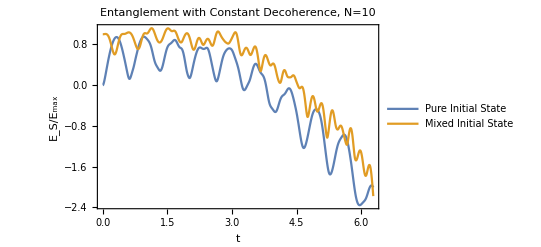

```mathematica
rho$mixed[5.8]//MatrixForm

lamb$mixed[t_]:=Eigenvalues[rho$mixed[t]];
entanglement$mixed[t_]:=If[t==0,0,-(lamb$mixed[t].Log[Np+1,lamb$mixed[t]])];
lamb$pure[t_]:=Eigenvalues[rho$pure[t]];
entanglement$pure[t_]:=If[t==0,0,-(lamb$pure[t].Log[Np+1,lamb$pure[t]])];Plot[{entanglement$pure[t],entanglement$mixed[t]},{t,0,tmax},PlotLabel->"Entanglement with Constant Decoherence, N=10",FrameLabel->{"t","E_S/E_max"},PlotLegends->{"Pure Initial State","Mixed Initial State"}]
```